### Rogers model and HIREC

```mathematica
WS=w0+Qt b;
WI=w0+s b-c;
Qt=(1-u)((1-p)s+p Qtm1);
```

```mathematica
Solve[{WS==WI,Qt==Qtm1},{p,Qtm1}]
```

{{p→(-c+b s u)/(c (-1+u)),Qtm1→(-c+b s)/b}}

```mathematica
phat=(-c+b s u)/(c (-1+u));
```

```mathematica
FullSimplify[phat/(1-phat)]
```

-(c-b s u)/(c u-b s u)

```mathematica
(* post HIREC *)
```

```mathematica
QQt = (1-uu)((1-phat)ss+phat QQtm1);
```

```mathematica
Simplify[Solve[QQt==QQtm1,QQtm1]]
```

{{QQtm1→-((c-b s) ss u (-1+uu))/(c (u-uu)+b s u (-1+uu))}}

```mathematica
Simplify[-((c-b s) ss u (-1+uu))/(c (u-uu)+b s u (-1+uu))/.{b->B c}]
```

((-1+B s) ss u (-1+uu))/(u+B s u (-1+uu)-uu)

```mathematica
hatQQ=((-1+B s) ss u (-1+uu))/(u+B s u (-1+uu)-uu);
```

```mathematica
hatQ=s-1/B;
```

```mathematica
Simplify[hatQQ/hatQ]
```

(B ss u (-1+uu))/(u+B s u (-1+uu)-uu)

```mathematica
(* fitness difference post-pre HIREC *)
```

```mathematica
Wp=w0+(1-phat)(s b-c)+phat Q b/.Q->s-(c/b);
WWp=w0+(1-phat)(ss bb-cc)+phat QQ bb/.QQ->hatQQ/.B->b/c;
```

```mathematica
Simplify[WWp-Wp]
```

((c-b s) (c^2 (-1+u) (u-uu)-b cc s u^2 (-1+uu)+c u (bb ss (-1+u)+b s (-1+u) (-1+uu)+cc (-u+uu))))/(c (-1+u) (c (u-uu)+b s u (-1+uu)))

```mathematica
Simplify[Solve[WWp-Wp==0,ss]]
```

{{ss→-((c (-1+u)-cc u) (c (u-uu)+b s u (-1+uu)))/(bb c (-1+u) u)}}

```mathematica
Simplify[-((c (-1+u)-cc u) (c (u-uu)+b s u (-1+uu)))/(bb c (-1+u) u)/.{bb->b,cc->c}]
```

(c (u-uu)+b s u (-1+uu))/(b (-1+u) u)

```mathematica
FullSimplify[Expand[hatQQ-hatQ]]
```

-((-1+B s) (u+B (s-ss) u (-1+uu)-uu))/(B (u+B s u (-1+uu)-uu))

```mathematica
(* try plotting regions where fitness increases after REC *)
```

```mathematica
?RegionPlot
```

RegionPlot[pred,{x,x_min,x_max},{y,y_min,y_max}] makes a plot showing the region in which pred is True.

0.888889

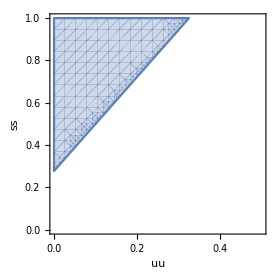

```mathematica
subs={cc->c,bb->b,b->4,c->1,u->0.1,s->0.5};
K=WWp-Wp//.subs;
phat/.subs
RegionPlot[K>0,{uu,0,0.5},{ss,0,1},FrameLabel->{uu,ss}]
```

```mathematica
K=(WWp-Wp)/.{bb->b,cc->c};
Simplify[Reduce[{K>0,s b>c>0,0<u<1,0<uu<1,0<s<1,0<ss<1},Reals],{s b>c>0,0<u<1,0<uu<1,0<s<1,0<ss<1,u s b/c<1}]
```

(u<uu&&((1+ss u==ss+uu&&((b>(c (u-uu))/(u (s+ss (-1+u)-s uu))&&(ss u)/uu≤s<(ss (-1+u))/(-1+uu))||s uu<ss u))||(b>(c (u-uu))/(u (s+ss (-1+u)-s uu))&&(((ss u)/uu<s<(ss (-1+u))/(-1+uu)&&ss+uu<1+ss u)||1+ss u<ss+uu))||(1+ss u<ss+uu&&s uu<ss u)||(ss+uu<1+ss u&&s uu≤ss u)))||(u==uu&&s+ss u<ss+s uu)||(uu<u&&(s+ss u≤ss+s uu||(b<(c (u-uu))/(u (s+ss (-1+u)-s uu))&&(s uu<ss u||ss u≥uu)&&ss+s uu<s+ss u)))